Fig. S1F-H

Generates plots showing that excluding simulations with numerical stiffness does not artificially bias diversity statistics (see SI Section 3).

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];

Needs["ErrorBarLogPlots`"];
```

### get color scheme data

```mathematica
(*Read in the numerical data*)Get["https://pastebin.com/raw/gN4wGqxe"]
ParulaCM=With[{colorlist=RGBColor@@@parulaColors},Blend[colorlist,#]&];
Cube1CM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
CubeYFCM=With[{colorlist=RGBColor@@@cubeYFColors},Blend[colorlist,#]&];
LinearLCM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
JetCM=With[{colorlist=RGBColor@@@jetColors},Blend[colorlist,#]&];
```

### import and process data: stiffness filtered

```mathematica
filename="data\\lDiversity_s1pt5";
```

```mathematica
params=Import[filename<>"_epsilonSet.mx"];
epsilon=Table[params[[i,1]]^2/params[[i,2]],{i,9}];
numConditions=Length[epsilon];
```

```mathematica
allStrats=Import[filename<>"_strats.mx"];
allFP=Import[filename<>"_allFP.mx"];
```

```mathematica
lengths=Length/@allFP;
```

```mathematica
validFPIndices=Position[lengths,x_/;x==10];
```

```mathematica
(*delete cases that failed*)
```

```mathematica
validFP=allFP[[validFPIndices//Flatten]];
```

```mathematica
propFP=Table[validFP[[i,j]]/Total[validFP[[i,j]]],{i,Length[validFP]},{j,numConditions+1}];
propFP=propFP[[1;;500]];
```

```mathematica
rankedPropFP=Table[ReverseSort[propFP[[i,j]]],{i,Length[propFP]},{j,numConditions+1}];
rankedPropFP=rankedPropFP[[1;;500]];
```

### import uniform sampling data

```mathematica
uniformData=Import["data\\stiffnessCheck_pbc_m10_s1=0.5_d=1_l=Sqrt[10]_fixedPoints_trajectories_alphas.mx"];
```

```mathematica
uniformFP=uniformData[[1]];
```

```mathematica
uniformProp=Table[uniformFP[[i]]/Total[uniformFP[[i]]],{i,2000}];
```

### entropy

```mathematica
shannonEntropy[n_]:=
Module[{},
modN=n/.{x_/;x<0->0};
entropyTable=Table[-modN[[i]]*Log[modN[[i]]],{i,Length[modN]}]//Quiet;
entropyTable2=entropyTable/.{Indeterminate->0};
entropy=entropyTable2//Total
]
```

```mathematica
entropies=Table[shannonEntropy[propFP[[i,j]]],{i,Length[propFP]},{j,numConditions+1}];
```

```mathematica
uniformEntropies=Table[shannonEntropy[uniformProp[[i]]],{i,2000}];
```

### effective species

```mathematica
effectiveSpecies=Table[E^shannonEntropy[propFP[[i,j]]],{i,Length[propFP]},{j,numConditions+1}];
```

```mathematica
uniformEffectiveSpecies=Table[E^uniformEntropies[[i]],{i,2000}];
```

### checking that the accepted strategies are representative

```mathematica
validStrats=allStrats[[validFPIndices//Flatten]];
```

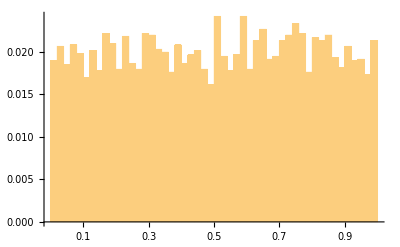

```mathematica
Histogram[validStrats//Flatten,{.02},"Probability",Ticks->{Range[.1,1,.1],Automatic},TicksStyle->Directive[Black,FontSize->12]]
```

```mathematica
Export["figS1F_strategyDistribution.svg",%];
```

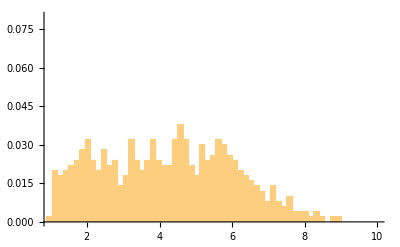

```mathematica
Histogram[effectiveSpecies[[;;,7]],{.15},"Probability",PlotRange->{{1,10},{0,.08}},TicksStyle->Directive[Black,FontSize->12]]
```

```mathematica
Export["figS1G_effectiveSpecies_figureData.svg",%];
```

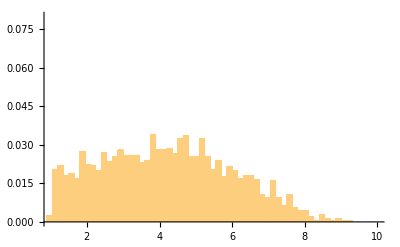

```mathematica
Histogram[uniformEffectiveSpecies,{.15},"Probability",PlotRange->{{1,10},{0,.08}},TicksStyle->Directive[Black,FontSize->12]]
```

```mathematica
Export["figS1H_effectiveSpecies_uniformSampling.svg",%];
```

```mathematica
KolmogorovSmirnovTest[uniformEffectiveSpecies,effectiveSpecies[[;; ,7]]]
```

0.776363